# Kim Polynomial Coefficients Solver

## BYU GR Research Group

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
howBig[x_]:=Module[{},UnitConvert[Quantity[ByteCount[x],"Bytes"],"Gigabytes"]//N]
(*DumpSave["filename.mx","Global`varname"];*)
```

# P4 (A4) Scheme

## Initialization

This code for the P4 follows the procedure in Section 2.2 of Kim (2024).

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0 γ_01
1
γ_21
β
0
0
0 γ_02
γ_12
1
α
γ_24
0
0 0
γ_13
γ_23
1
γ_23
γ_13
0 0
0
γ_24
α
1
γ_12
γ_02 0
0
0
β
γ_21
1
γ_01 0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
-a_3
-a_26
-a_16
-a_06 a_01
a_11
a_21
-a_2
-a_25
-a_15
-a_05 a_02
a_12
a_22
-a_1
-a_24
-a_14
-a_04 a_03
a_13
a_23
0
-a_23
-a_13
-a_03 a_04
a_14
a_24
a_1
-a_22
-a_12
-a_02 a_05
a_15
a_25
a_2
-a_21
-a_11
-a_01 a_06
a_16
a_26
a_3
-a_20
-a_10
-a_00)

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
interiorCoeffsP4={α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
(*Get["P4_bdCoeffs0.mx"]
Get["P4_bdCoeffs1.mx"]
Get["P4_bdCoeffs2.mx"]*)
```

## General Extrapolation Polynomial

The only settings the user should have to change for a different (first derivative) scheme are:
	- LHSBandCount
	- n
	- freeInteriorPars
	- yDeriv
For the P4 (A4) scheme, we have:
	LHSBandCount = 5
	n = 4
	freeInteriorPars = 3
	yDeriv = 8

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=4; (*order of the scheme*)
freeInteriorPars=3; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=8; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576 | 53248
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764 | 6908733
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648 | 218103808
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500 | 3173828125
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 40320 | 362880 yHat | 1814400 yHat^2 | 6652800 yHat^3 | 19958400 yHat^4 | 51891840 yHat^5) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13) = (f0
f1
f2
f3
f4
f5
f6
fp0
fp1
fp2
fp3
fp4
fp5
0)

Singularities:
(yHat→1.23232
yHat→2.01136
yHat→2.75838
yHat→3.50832
yHat→4.33577)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList2 in terms of the optimization free parameter ŷ
Variables:
	fVars2: List of f_i and f_i' variables that will appear in the shifted stencil for Node 2
	bdCoeffsList2: List of boundary coefficients that will appear in the shifted stencil for Node 2
	schemeShifted: The shifted scheme for Node 2 (Kim 2024 Eq. 13a)
	schemeCentered: The centered scheme for Node 2 in terms of the extrapolation polynomial P(x) (Kim 2024 Eq. 12a)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode3: The scheme for Node 3, which only depends on interiorCoeffsP4
	SOLfp5: The solution to Node 3’s scheme equation for f_5' in terms of fVars2
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs2: System of equations with each of the coefficient terms equal to each other
	bdCoeffs2: Solution to the system of equations for bdCoeffsList2 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars2 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars2 as well as f_5'. We eliminate the dependence on f_5' by using Node 3’s scheme to solve for f_5' in terms of fVars2.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars2, we construct a system of equations by equating the coefficient in front of each term of fVars2 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList2 in terms of interiorCoeffsP4 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_22=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_22 so that bdCoeffsList2 and fVars2 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs2 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 1 and Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 3 for f_5' in terms of the other fVars, we must also do the same for f_4' (Nodes 1 and 0) and f_3' (Node 0) using Nodes 2 and 1, respectively.

### Node 2

```mathematica
(*----------STEP 1----------*)
fVars2={fp0,fp1,fp2,fp3,fp4,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26};
schemeShifted=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)
schemeCentered=β fp0+α fp1+fp2+α fp3+β fp4-(-a3 P[-1]-a2 f0-a1 f1+a1 f3+a2 f4+a3 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsP4;
schemeCentered=schemeCentered/.SOLfp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsP4;

(*----------STEP 5----------*)
(*DumpSave["P4_bdCoeffs2.mx","Global`bdCoeffs2"]*)
```

### Node 1

```mathematica
(*----------STEP 1----------*)
fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16};
schemeShifted=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)
schemeCentered=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a3 P[-2]-a2 P[-1]-a1 f0+a1 f2+a2 f3+a3 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;

SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsP4;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfp5/.SOLfp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsP4;

(*----------STEP 5----------*)
(*DumpSave["P4_bdCoeffs1.mx","Global`bdCoeffs1"]*)
```

### Node 0

```mathematica
(*----------STEP 1----------*)
fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06};
schemeShifted=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)
schemeCentered=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a3 P[-3]-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2+a3 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;
schemeNode1=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6;

SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsP4;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
SOLfp3=Solve[schemeNode1,fp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfp5/.SOLfp4/.SOLfp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsP4;

(*----------STEP 5----------*)
(*DumpSave["P4_bdCoeffs0.mx","Global`bdCoeffs0"]*)
```

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0;
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ];
κBar2Re[κ_]=(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ-κBar2Norm[κ])^2;
```

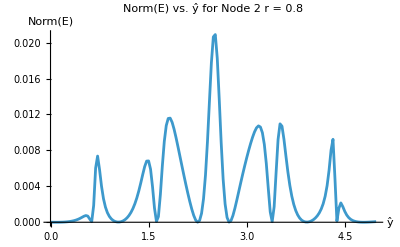

Evaluation time: 19.043422

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a21 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

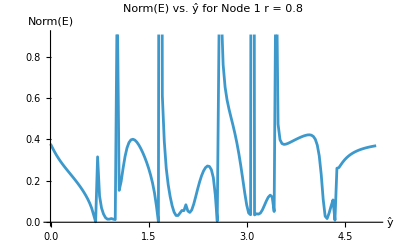

Evaluation time: 29.597653

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

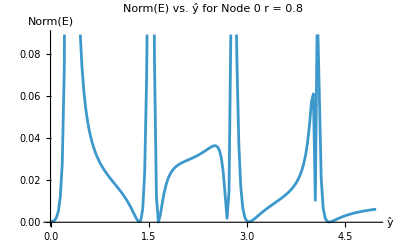

Evaluation time: 316.275076

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

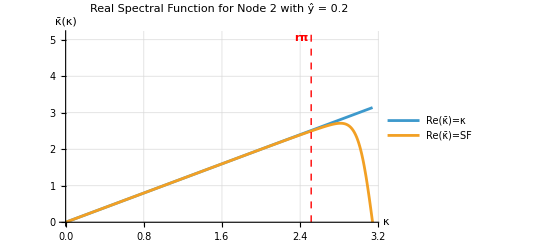

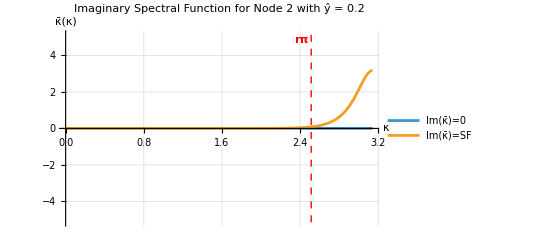

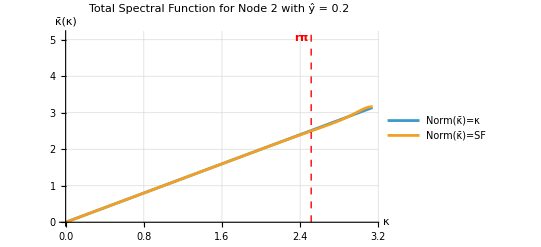

```mathematica
r=0.8;
yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat=yHat2List[[1]];
Plot[{κ,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

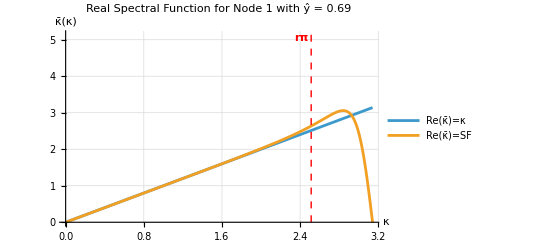

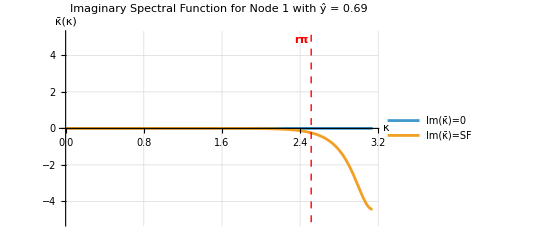

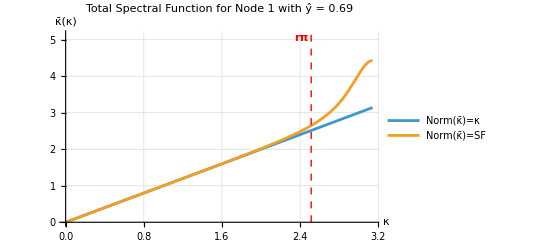

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat=yHat1List[[1]];
Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

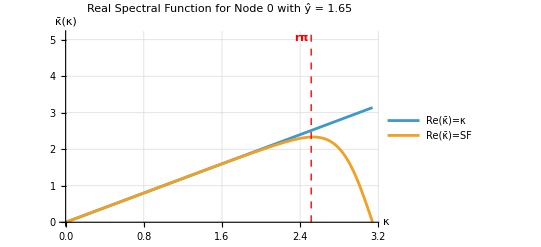

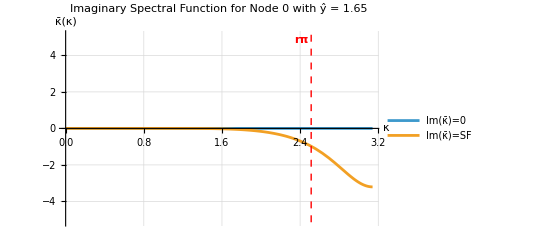

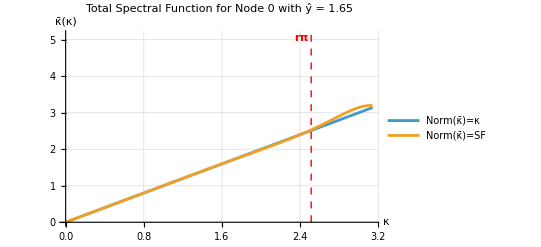

```mathematica
r=0.8;
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26}; (*old and wrong i think*)
yHat0List={(*1*)1.35,(*2*)1.65,(*3*)2.70,(*4*)3.03,(*5*)4.26}; (*new*)
yHat=yHat0List[[1]];
Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};

yHat2=yHat2List[[9]];
yHat1=yHat1List[[4]];
yHat0=yHat0List[[1]];

yHat0=1.89;
yHat1=1.65;
yHat2=1.14;
```

### Define Coefficients

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsP4/.{a1->a,a2->b,a3->c};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.577046,β→0.0890084,a→0.651708,b→0.248159,c→0.00600963,α12→9.8205,β12→10.2829,α21→0.0818506,α22→1.68906,β22→0.496148,β31→0.0179189,α31→0.335004,α32→0.754877,β32→0.136673,a1→-3.73445,b1→-10.7659,c1→11.1588,d1→3.89328,e1→-0.638984,f1→0.0958773,g1→-0.00859553,a2→-0.318509,b2→-1.39694,c2→0.536402,d2→1.12232,e2→0.0594506,f2→-0.00274384,g2→0.0000280668,a3→-0.0767036,b3→-0.627344,c3→-0.37834,d3→0.712846,e3→0.357225,f3→0.0128421,g3→-0.00052505}

### Nate Output

```mathematica
interiorNate=interiorCoeffsP4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.577046,β→0.0890084,a1→0.651708,a2→0.248159,a3→0.00600963,γ01→9.8205,γ02→10.2829,γ10→0.0818506,γ12→1.68906,γ13→0.496148,γ20→0.0179189,γ21→0.335004,γ23→0.754877,γ24→0.136673,a00→-3.73445,a01→-10.7659,a02→11.1588,a03→3.89328,a04→-0.638984,a05→0.0958773,a06→-0.00859553,a10→-0.318509,a11→-1.39694,a12→0.536402,a13→1.12232,a14→0.0594506,a15→-0.00274384,a16→0.0000280668,a20→-0.0767036,a21→-0.627344,a22→-0.37834,a23→0.712846,a24→0.357225,a25→0.0128421,a26→-0.00052505}

### Other Results

```mathematica
Kim24={α->0.5862704032801503,β->0.0954953355017055,a->0.6431406736919156,b->0.2586011023495066,c->0.007140953479797375,α12->43.65980335321481,β12->92.40143116322876,α21->0.08351537442980239,α22->1.961483362670730,β22->0.8789761422182460,β31->0.008073091519768687,α31->0.2162434143850924,α32->1.052242062502679,β32->0.2116022463346598,a1->-6.658527037451025,b1->-86.92242000231872,c1->47.58661913475775,d1->57.30693626084370,e1->-13.71254216556246,f1->2.659826729790792,g1->-0.2598929200600359,a2->-0.3199960780333493,b2->-1.438068456255548,c2->0.07735499170041915,d2->1.496612372811008,e2->0.2046919801608821,f2->-0.02229717539815850,g2->0.001702365014746567,a3->-0.03644974757120792,b3->-0.4997030280694729,c3->-0.7861024376433451,d3->0.7439822445654316,e3->0.5629384925762924,f3->0.01563884275691290,g3->-0.0003043666146108995};
HAMR={α->0.5747612151,β->0.0879324249,a->1.3069171114/2,b->0.9828406281/4,c->0.0356295405/6,α12->9.4133049605,β12->10.7741034803,α21->0.1023343303,α22->1.8854940182,β22->0.8582327249,β31->0.0347468867,α31->0.4064246796,α32->0.7683583302,β32->0.1623349133,a1->-3.6882535854000005,b1->-10.3169611301,c1->9.6807767746,d1->5.4529053045,e1->-1.5191959829,f1->0.4834876759,g1->-0.0927590566,a2->-0.3586079596,b2->-1.3424668425,c2->0.0834751059,d2->1.4235697122,e2->0.2245783548,f2->-0.0358453729,g2->0.0052970021,a3->-0.1274311870,b3->-0.6299599564,c3->-0.3024922988999999,d3->0.6498856630,e3->0.3919470424,f3->0.0189402158,g3->-0.0008894789};
coeff=Kim24;
```

#### Kim 07 Modified Boundary Coefficients

Why is Kim 07 different than HAMR for modifying the coeffs for eigenvalue analysis? (eqs 41-45)

```mathematica
Kim07={α->0.5862704032801503,β->0.0954953355017055,a1->0.6431406736919156,a2->0.2586011023495066,a3->0.007140953479797375,γ01->5.912678614078549,γ02->3.775623951744012,γ10->0.08360703307833438,γ12->2.058102869495757,γ13->0.9704052014790193,γ20->0.03250008295108466,γ21->0.3998040493524358,γ23->0.7719261277615860,γ24->0.1626635931256900,a00->-3.240681563472493,a01->-3.456878182643609,a02->5.839043358834730,a03->1.015886726041007,a04->-0.2246526470654333,a05->0.08564940889936562,a06->-0.01836710059356763,a10->-0.3177447290722621,a11->-1.468827048894462,a12->-0.02807631929593225,a13->1.593461635747659,a14->0.2533027046976367,a15->-0.03619652460174756,a16->0.004080281419108407,a20->-0.1219006056449124,a21->-0.6301651351188667,a22->-0.3119603043096557,a23->0.6521195063966084,a24->0.3938843551210350,a25->0.01904944407973912,a26->-0.001027260523947668};
```

```mathematica
{γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.Kim07),
γ13Bar->(γ13/(1-γ10*γ01)/.Kim07),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.Kim07),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.Kim07),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.Kim07)};

Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.Kim07;
Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.Kim07;

barCoeffs=Join[%,%%,%%%]
```

{a21Bar→-0.296033,a22Bar→-1.50549,a23Bar→0.16354,a24Bar→1.47735,a25Bar→0.165628,a26Bar→-0.0130691,a11Bar→-2.33321,a12Bar→-1.02097,a13Bar→2.98329,a14Bar→0.538081,a15Bar→-0.0857445,a16Bar→0.0111061,γ12Bar→3.44587,γ13Bar→1.91909,γ21Bar→0.0554085,γ23Bar→1.97387,γ24Bar→0.813458}

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.Kim07)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 3.44587 | 1.91909 | 0 | 0 | 0 | 0 | 0 | 0
0.0554085 | 1 | 1.97387 | 0.813458 | 0 | 0 | 0 | 0 | 0
0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0
0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0
0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0
0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0
0 | 0 | 0 | 0 | 0.162664 | 0.771926 | 1 | 0.399804 | 0.0325001
0 | 0 | 0 | 0 | 0 | 0.970405 | 2.0581 | 1 | 0.083607
0 | 0 | 0 | 0 | 0 | 0 | 3.77562 | 5.91268 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.Kim07)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-2.33321 | -1.02097 | 2.98329 | 0.538081 | -0.0857445 | 0.0111061 | 0 | 0 | 0
-0.296033 | -1.50549 | 0.16354 | 1.47735 | 0.165628 | -0.0130691 | 0 | 0 | 0
-0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0
-0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0
0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0
0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095
0 | 0 | 0.00102726 | -0.0190494 | -0.393884 | -0.65212 | 0.31196 | 0.630165 | 0.121901
0 | 0 | -0.00408028 | 0.0361965 | -0.253303 | -1.59346 | 0.0280763 | 1.46883 | 0.317745
0 | 0 | 0.0183671 | -0.0856494 | 0.224653 | -1.01589 | -5.83904 | 3.45688 | 3.24068)

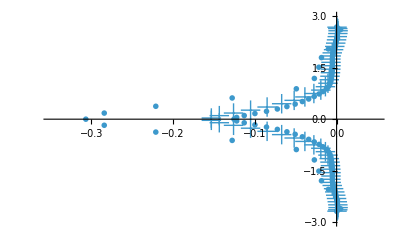

```mathematica
k=21;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n21=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["◯",8]];

k=60;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n60=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["+",20]];

k=81;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n81=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["·",36]];

Show[n21,n60,n81,PlotRange->{{-0.35,0.05},{-3,3}}]
```

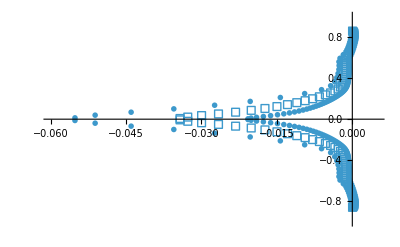

```mathematica
k=50;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat]/π;

n50=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["⊲",8]];

k=100;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat]/π;

n100=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["□",8]];

k=200;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat]/π;

n200=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["◯",6]];

Show[n50,n100,n200,PlotRange->{{-0.06,0.005},{-1,1}}]
```

#### Kim 24 Modified Boundary Coefficients

```mathematica
Kim24={α->0.5862704032801503,β->0.0954953355017055,a1->0.6431406736919156,a2->0.2586011023495066,a3->0.007140953479797375,γ01->43.65980335321481,γ02->92.40143116322876,γ10->0.08351537442980239,γ12->1.961483362670730,γ13->0.8789761422182460,γ20->0.008073091519768687,γ21->0.2162434143850924,γ23->1.052242062502679,γ24->0.2116022463346598,a00->-6.658527037451025,a01->-86.92242000231872,a02->47.58661913475775,a03->57.30693626084370,a04->-13.71254216556246,a05->2.659826729790792,a06->-0.2598929200600359,a10->-0.3199960780333493,a11->-1.438068456255548,a12->0.07735499170041915,a13->1.496612372811008,a14->0.2046919801608821,a15->-0.02229717539815850,a16->0.001702365014746567,a20->-0.03644974757120792,a21->-0.4997030280694729,a22->-0.7861024376433451,a23->0.7439822445654316,a24->0.5629384925762924,a25->0.01563884275691290,a26->-0.0003043666146108995};
```

```mathematica
{γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.Kim24),
γ13Bar->(γ13/(1-γ10*γ01)/.Kim24),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.Kim24),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.Kim24),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.Kim24)};

Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.Kim24;
Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.Kim24;

barCoeffs=Join[%,%%,%%%]
```

{a21Bar→-0.445082,a22Bar→-0.979255,a23Bar→0.739533,a24Bar→0.670234,a25Bar→0.0219576,a26Bar→-0.000578643,a11Bar→-2.19981,a12Bar→1.47259,a13Bar→1.24303,a14Bar→-0.510115,a15Bar→0.0923693,a16Bar→-0.00884546,γ12Bar→2.17494,γ13Bar→-0.332157,γ21Bar→0.147555,γ23Bar→1.19359,γ24Bar→0.261111}

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.Kim24)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 2.17494 | -0.332157 | 0 | 0 | 0 | 0 | 0 | 0
0.147555 | 1 | 1.19359 | 0.261111 | 0 | 0 | 0 | 0 | 0
0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0
0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0
0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0
0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0
0 | 0 | 0 | 0 | 0.211602 | 1.05224 | 1 | 0.216243 | 0.00807309
0 | 0 | 0 | 0 | 0 | 0.878976 | 1.96148 | 1 | 0.0835154
0 | 0 | 0 | 0 | 0 | 0 | 92.4014 | 43.6598 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@RHS[k]
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

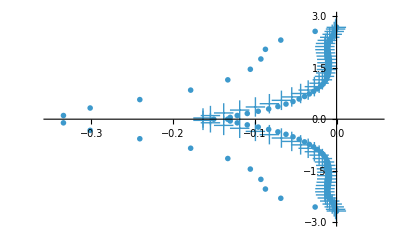

```mathematica
k=21;
LHSNum=(LHS[k]/.Kim24)/.barCoeffs;
RHSNum=(RHS[k]/.Kim24)/.barCoeffs;
RHSNum[[All,1]]=RHSNum[[All,1]]*(1-r)/.{r->0.7};

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n21=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.35,0.05},{-3,3}},PlotMarkers->Style["◯",8]];

k=60;
LHSNum=(LHS[k]/.Kim24)/.barCoeffs;
RHSNum=(RHS[k]/.Kim24)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n60=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.35,0.05},{-3,3}},PlotMarkers->Style["+",20]];

k=81;
LHSNum=(LHS[k]/.Kim24)/.barCoeffs;
RHSNum=(RHS[k]/.Kim24)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n81=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.35,0.05},{-3,3}},PlotMarkers->Style["·",36]];

Show[n21,n60,n81]
```

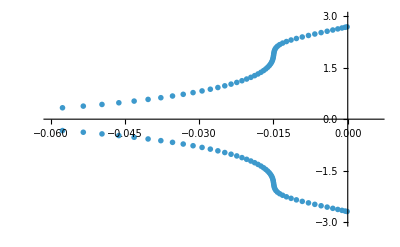

```mathematica
k=121;
LHSNum=(LHS[k]/.Kim24)/.barCoeffs;
RHSNum=(RHS[k]/.Kim24)/.barCoeffs;
RHSNum[[All,1]]=RHSNum[[All,1]]*(1-r)/.{r->0.7};

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.06,0.006},{-3,3}},PlotMarkers->Style["Δ",8]]
```

```mathematica
LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32}
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1},
{a2,b2,c2,d2,e2,f2,g2},
{a3,b3,c3,d3,e3,f3,g3}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
]

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]
```

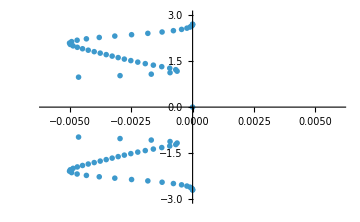

```mathematica
nList={21,60,81};
nList={121};
plotList={};
For[k=1,k<=Length@nList,k++,
n=nList[[k]];
LHS=LHSMatrix[n,3,coeff];
RHS=RHSMatrix[n,3,coeff];
(*Print[MatrixForm@Normal@RHS];*)
RHS[[All,1]]=RHS[[All,1]]*(1-0.7);
(*Print[MatrixForm@Normal@RHS];*)

(*For[j=1,j<=n,j++,LHS[[1,j]]=0];
For[j=1,j<=n,j++,LHS[[j,1]]=0];
For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[j,1]]=0];
LHS[[1,1]]=1;*)
(*For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[n,j]]=0];
For[j=1,j<=n,j++,RHS[[n-1,j]]=0];*)
LHS//MatrixForm;
RHS//MatrixForm;
(*Print[LHS//MatrixForm];
Print[RHS//MatrixForm];*)

mat=Inverse[LHS].RHS;
eigs=-Eigenvalues[mat];

AppendTo[plotList,ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["Δ",8],PlotRange->{{-0.006,0.006},{-3,3}},ImageSize->Medium]]
]
plotList
```

#### HAMR 08 Modified Boundary Coefficients

```mathematica
HAMR2={α->0.5747612151,β->0.0879324249,a1->1.3069171114/2,a2->0.9828406281/4,a3->0.0356295405/6,γ01->9.4133049605,γ02->10.7741034803,γ10->0.1023343303,γ12->1.8854940182,γ13->0.8582327249,γ20->0.0347468867,γ21->0.4064246796,γ23->0.7683583302,γ24->0.1623349133,a00->-3.6882535854000005,a01->-10.3169611301,a02->9.6807767746,a03->5.4529053045,a04->-1.5191959829,a05->0.4834876759,a06->-0.0927590566,a10->-0.3586079596,a11->-1.3424668425,a12->0.0834751059,a13->1.4235697122,a14->0.2245783548,a15->-0.0358453729,a16->0.0052970021,a20->-0.1274311870,a21->-0.6299599564,a22->-0.3024922988999999,a23->0.6498856630,a24->0.3919470424,a25->0.0189402158,a26->-0.0008894789};
γ03=0;
γ04=0;
```

```mathematica
{γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.HAMR2),
γ13Bar->((γ13-γ03*γ10)/(1-γ10*γ01)/.HAMR2),
γ21Bar->((γ21-γ01*γ20)/(1-γ20*γ02)/.HAMR2),
γ23Bar->((γ23-γ03*γ20)/(1-γ20*γ02)/.HAMR2),
γ24Bar->((γ24-γ04*γ20)/(1-γ20*γ02)/.HAMR2)};

Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.HAMR2;
Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(1-γ20*γ02)*(ToExpression@StringJoin["a2",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ20),
{j,1,6}]/.HAMR2;

barCoeffs=Join[%,%%,%%%]
```

{a21Bar→-0.433924,a22Bar→-1.02116,a23Bar→0.735917,a24Bar→0.710855,a25Bar→0.00342137,a26Bar→0.00372999,a11Bar→-7.81256,a12Bar→-24.7222,a13Bar→23.5872,a14Bar→10.3566,a15Bar→-2.32514,a16Bar→0.403029,γ12Bar→21.3358,γ13Bar→23.3878,γ21Bar→0.126818,γ23Bar→1.22813,γ24Bar→0.259473}

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.HAMR2)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 21.3358 | 23.3878 | 0 | 0 | 0 | 0 | 0 | 0
0.126818 | 1 | 1.22813 | 0.259473 | 0 | 0 | 0 | 0 | 0
0.0879324 | 0.574761 | 1 | 0.574761 | 0.0879324 | 0 | 0 | 0 | 0
0 | 0.0879324 | 0.574761 | 1 | 0.574761 | 0.0879324 | 0 | 0 | 0
0 | 0 | 0.0879324 | 0.574761 | 1 | 0.574761 | 0.0879324 | 0 | 0
0 | 0 | 0 | 0.0879324 | 0.574761 | 1 | 0.574761 | 0.0879324 | 0
0 | 0 | 0 | 0 | 0.162335 | 0.768358 | 1 | 0.406425 | 0.0347469
0 | 0 | 0 | 0 | 0 | 0.858233 | 1.88549 | 1 | 0.102334
0 | 0 | 0 | 0 | 0 | 0 | 10.7741 | 9.4133 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.HAMR2)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-7.81256 | -24.7222 | 23.5872 | 10.3566 | -2.32514 | 0.403029 | 0 | 0 | 0
-0.433924 | -1.02116 | 0.735917 | 0.710855 | 0.00342137 | 0.00372999 | 0 | 0 | 0
-0.24571 | -0.653459 | 0 | 0.653459 | 0.24571 | 0.00593826 | 0 | 0 | 0
-0.00593826 | -0.24571 | -0.653459 | 0 | 0.653459 | 0.24571 | 0.00593826 | 0 | 0
0 | -0.00593826 | -0.24571 | -0.653459 | 0 | 0.653459 | 0.24571 | 0.00593826 | 0
0 | 0 | -0.00593826 | -0.24571 | -0.653459 | 0 | 0.653459 | 0.24571 | 0.00593826
0 | 0 | 0.000889479 | -0.0189402 | -0.391947 | -0.649886 | 0.302492 | 0.62996 | 0.127431
0 | 0 | -0.005297 | 0.0358454 | -0.224578 | -1.42357 | -0.0834751 | 1.34247 | 0.358608
0 | 0 | 0.0927591 | -0.483488 | 1.5192 | -5.45291 | -9.68078 | 10.317 | 3.68825)

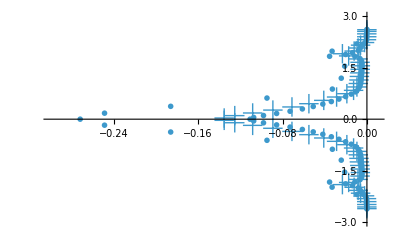

```mathematica
k=21;
LHSNum=(LHS[k]/.HAMR2)/.barCoeffs;
RHSNum=(RHS[k]/.HAMR2)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n21=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.3,0.01},{-3,3}},PlotMarkers->Style["◯",8]];

k=60;
LHSNum=(LHS[k]/.HAMR2)/.barCoeffs;
RHSNum=(RHS[k]/.HAMR2)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n60=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.3,0.01},{-3,3}},PlotMarkers->Style["+",20]];

k=81;
LHSNum=(LHS[k]/.HAMR2)/.barCoeffs;
RHSNum=(RHS[k]/.HAMR2)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n81=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.3,0.01},{-3,3}},PlotMarkers->Style["·",36]];

Show[n21,n60,n81]
```

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2]
```

{γ12Bar→4.31939,γ13Bar→2.52897,γ21Bar→0.184191,γ23Bar→1.02544,γ24Bar→0.216864,a11Bar→-2.62888,a12Bar→-1.9214,a13Bar→4.09637,a14Bar→0.569623,a15Bar→-0.0539869,a16Bar→0.0037292,a17Bar→5.09721 (-0.0818506 a07+a17),a18Bar→5.09721 (-0.0818506 a08+a18),a21Bar→-0.51017,a22Bar→-0.786652,a23Bar→0.741235,a24Bar→0.546167,a25Bar→0.0213301,a26Bar→-0.000842862,a27Bar→19.3857 (-0.0179189 a17+0.0818506 a27),a28Bar→19.3857 (-0.0179189 a18+0.0818506 a28)}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 4.31939 | 2.52897 | 0 | 0 | 0 | 0 | 0 | 0
0.184191 | 1 | 1.02544 | 0.216864 | 0 | 0 | 0 | 0 | 0
0.0890084 | 0.577046 | 1 | 0.577046 | 0.0890084 | 0 | 0 | 0 | 0
0 | 0.0890084 | 0.577046 | 1 | 0.577046 | 0.0890084 | 0 | 0 | 0
0 | 0 | 0.0890084 | 0.577046 | 1 | 0.577046 | 0.0890084 | 0 | 0
0 | 0 | 0 | 0.0890084 | 0.577046 | 1 | 0.577046 | 0.0890084 | 0
0 | 0 | 0 | 0 | 0.136673 | 0.754877 | 1 | 0.335004 | 0.0179189
0 | 0 | 0 | 0 | 0 | 0.496148 | 1.68906 | 1 | 0.0818506
0 | 0 | 0 | 0 | 0 | 0 | 10.2829 | 9.8205 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | 0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | 0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | 0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-2.62888 | -1.9214 | 4.09637 | 0.569623 | -0.0539869 | 0.0037292 | 0 | 0 | 0 | 0 | 0
-0.51017 | -0.786652 | 0.741235 | 0.546167 | 0.0213301 | -0.000842862 | 0 | 0 | 0 | 0 | 0
-0.248159 | -0.651708 | 0 | 0.651708 | 0.248159 | 0.00600963 | 0 | 0 | 0 | 0 | 0
-0.00600963 | -0.248159 | -0.651708 | 0 | 0.651708 | 0.248159 | 0.00600963 | 0 | 0 | 0 | 0
0 | -0.00600963 | -0.248159 | -0.651708 | 0 | 0.651708 | 0.248159 | 0.00600963 | 0 | 0 | 0
0 | 0 | -0.00600963 | -0.248159 | -0.651708 | 0 | 0.651708 | 0.248159 | 0.00600963 | 0 | 0
0 | 0 | 0 | -0.00600963 | -0.248159 | -0.651708 | 0 | 0.651708 | 0.248159 | 0.00600963 | 0
0 | 0 | 0 | 0 | -0.00600963 | -0.248159 | -0.651708 | 0 | 0.651708 | 0.248159 | 0.00600963
0 | 0 | 0 | 0 | 0.00052505 | -0.0128421 | -0.357225 | -0.712846 | 0.37834 | 0.627344 | 0.0767036
0 | 0 | 0 | 0 | -0.0000280668 | 0.00274384 | -0.0594506 | -1.12232 | -0.536402 | 1.39694 | 0.318509
0 | 0 | 0 | 0 | 0.00859553 | -0.0958773 | 0.638984 | -3.89328 | -11.1588 | 10.7659 | 3.73445)

### Plot Eigenvalue Spectra

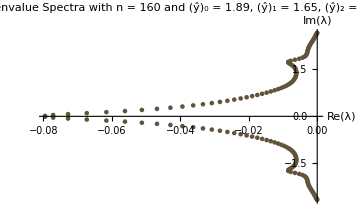

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsP4/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_P4","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP121R3DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.5770460201292381;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.08900836845092142;
		double a1 = 0.6517078440898839;
		double a2 = 0.24815882627035918;
		double a3 = 0.006009630649852392;
		double gamma01 = 9.82050086297005;
		double gamma02 = 10.282867809058313;
		double gamma10 = 0.08185064221829087;
		double gamma12 = 1.6890627481714804;
		double gamma13 = 0.4961478931388701;
		double gamma20 = 0.017918887158094664;
		double gamma21 = 0.33500390219730425;
		double gamma23 = 0.7548768581531722;
		double gamma24 = 0.13667343083285768;
		double a00 =  - 3.73445251380582;
		double a01 =  - 10.765902315893966;
		double a02 = 11.158777481815811;
		double a03 = 3.8932795799881186;
		double a04 =  - 0.6389839738157034;
		double a05 = 0.09587727397420936;
		double a06 =  - 0.008595531676508965;
		double a10 =  - 0.31850909623427476;
		double a11 =  - 1.396944235854646;
		double a12 = 0.5364016058704685;
		double a13 = 1.1223168928950014;
		double a14 = 0.059450604503400145;
		double a15 =  - 0.0027438380250710795;
		double a16 = 0.00002806684476978311;
		double a20 =  - 0.07670359108573083;
		double a21 =  - 0.6273443641711278;
		double a22 =  - 0.37833992259630045;
		double a23 = 0.7128462614236629;
		double a24 = 0.3572245284141374;
		double a25 = 0.012842138314361781;
		double a26 =  - 0.0005250502990408262;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06},
			{a10, a11, a12, a13, a14, a15, a16},
			{a20, a21, a22, a23, a24, a25, a26}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a3, -a2, -a1, 0.0, a1, a2, a3
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_P4_yHat0_1.89_yHat1_1.65_yHat2_1.14.h

# P4 (B4) Scheme

## a)

# P4 (C4) Scheme

## a)

# P6 (A6) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0 γ_01
1
γ_21
β
0
0
0 γ_02
γ_12
1
α
γ_24
0
0 0
γ_13
γ_23
1
γ_23
γ_13
0 0
0
γ_24
α
1
γ_12
γ_02 0
0
0
β
γ_21
1
γ_01 0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
-a_3
-a_26
-a_16
-a_06 a_01
a_11
a_21
-a_2
-a_25
-a_15
-a_05 a_02
a_12
a_22
-a_1
-a_24
-a_14
-a_04 a_03
a_13
a_23
0
-a_23
-a_13
-a_03 a_04
a_14
a_24
a_1
-a_22
-a_12
-a_02 a_05
a_15
a_25
a_2
-a_21
-a_11
-a_01 a_06
a_16
a_26
a_3
-a_20
-a_10
-a_00)

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
(*Note that these are found with the P6 Scheme NEW header in that notebook*)
interiorCoeffsA6={α->0.5573223518365282,β->0.076203478481807,a1->0.6694377318500324,a2->0.22598218207734894,a3->0.0040412447712016904};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["A6_bdCoeffs2.mx"];
Get["A6_bdCoeffs1.mx"];
Get["A6_bdCoeffs0.mx"];
```

## General Extrapolation Polynomial

For the P6 (A6) scheme, we have:
	LHSBandCount = 5
	n = 6
	freeInteriorPars = 2
	yDeriv = 10

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=2; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=10; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576 | 53248
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764 | 6908733
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648 | 218103808
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500 | 3173828125
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3628800 | 39916800 yHat | 239500800 yHat^2 | 1037836800 yHat^3) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13) = (f0
f1
f2
f3
f4
f5
f6
fp0
fp1
fp2
fp3
fp4
fp5
0)

Singularities:
(yHat→1.82898
yHat→2.7624
yHat→3.71631)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList2 in terms of the optimization free parameter ŷ
Variables:
	fVars2: List of f_i and f_i' variables that will appear in the shifted stencil for Node 2
	bdCoeffsList2: List of boundary coefficients that will appear in the shifted stencil for Node 2
	schemeShifted: The shifted scheme for Node 2
	schemeCentered: The centered scheme for Node 2 in terms of the extrapolation polynomial P(x)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode3: The scheme for Node 3, which only depends on interiorCoeffsP6
	SOLfp5: The solution to Node 3’s scheme equation for f_5' in terms of fVars2
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs2: System of equations with each of the coefficient terms equal to each other
	bdCoeffs2: Solution to the system of equations for bdCoeffsList2 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars2 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars2 as well as f_5'. We eliminate the dependence on f_5' by using Node 3’s scheme to solve for f_5' in terms of fVars2.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars2, we construct a system of equations by equating the coefficient in front of each term of fVars2 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList2 in terms of interiorCoeffsP4 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_22=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_22 so that bdCoeffsList2 and fVars2 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs2 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 1 and Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 3 for f_5' in terms of the other fVars, we must also do the same for f_4' (Nodes 1 and 0) and f_3' (Node 0) using Nodes 2 and 1, respectively.

### Node 2

```mathematica
(*----------STEP 1----------*)
fVars2={fp0,fp1,fp2,fp3,fp4,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26};
schemeShifted=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)
schemeCentered=β fp0+α fp1+fp2+α fp3+β fp4-(-a3 P[-1]-a2 f0-a1 f1+a1 f3+a2 f4+a3 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsA6;
schemeCentered=schemeCentered/.SOLfp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsA6;

(*----------STEP 5----------*)
(*DumpSave["A6_bdCoeffs2.mx","Global`bdCoeffs2"]*)
```

### Node 1

```mathematica
(*----------STEP 1----------*)
fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16};
schemeShifted=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)
schemeCentered=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a3 P[-2]-a2 P[-1]-a1 f0+a1 f2+a2 f3+a3 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;

SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsA6;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfp5/.SOLfp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsA6;

(*----------STEP 5----------*)
(*DumpSave["A6_bdCoeffs1.mx","Global`bdCoeffs1"]*)
```

### Node 0

```mathematica
(*----------STEP 1----------*)
fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06};
schemeShifted=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)
schemeCentered=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a3 P[-3]-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2+a3 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;
schemeNode1=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6;

SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsA6;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
SOLfp3=Solve[schemeNode1,fp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfp5/.SOLfp4/.SOLfp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsA6;

(*----------STEP 5----------*)
(*DumpSave["A6_bdCoeffs0.mx","Global`bdCoeffs0"]*)
```

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0;
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ];
κBar2Re[κ_]=(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ-κBar2Norm[κ])^2;
```

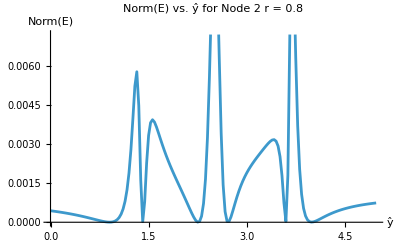

Evaluation time: 11.164861

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

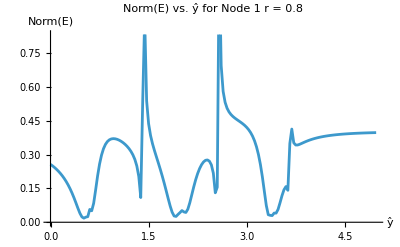

Evaluation time: 12.156572

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

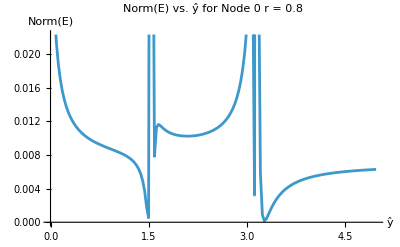

Evaluation time: 68.0821107

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

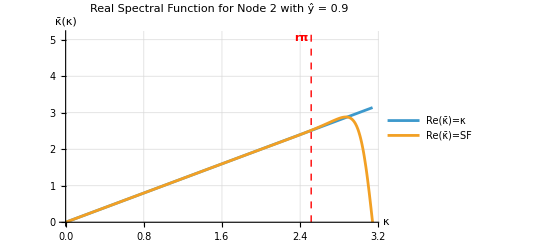

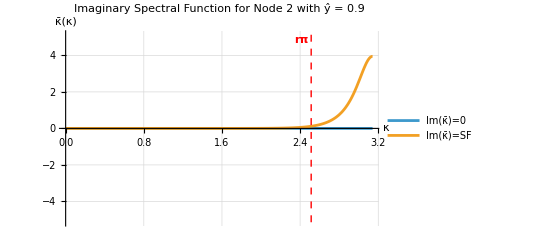

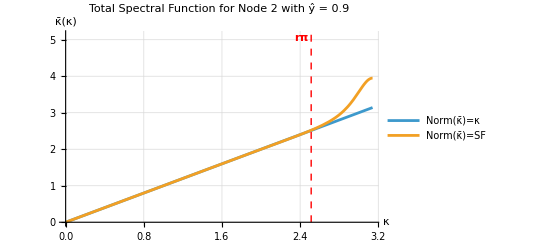

```mathematica
r=0.8;
yHat2List={(*1*)0.90,(*2*)1.41,(*3*)2.25,(*4*)2.73,(*5*)3.60,(*6*)3.99};
yHat=yHat2List[[1]];
Plot[{κ,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

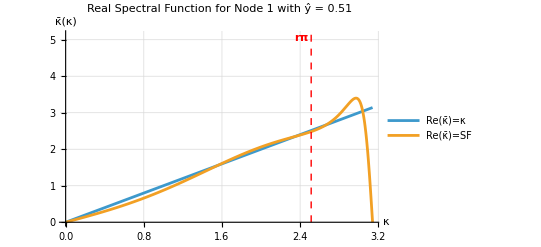

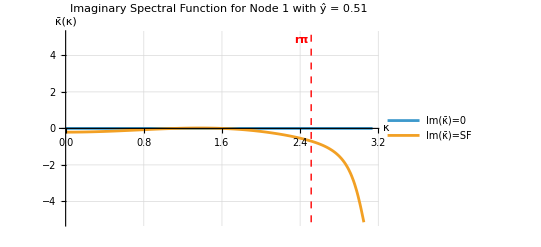

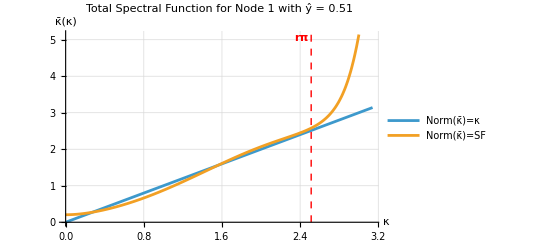

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)0.51,(*2*)1.38,(*3*)1.92,(*4*)2.52,(*5*)3.39};
yHat=yHat1List[[1]];
Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

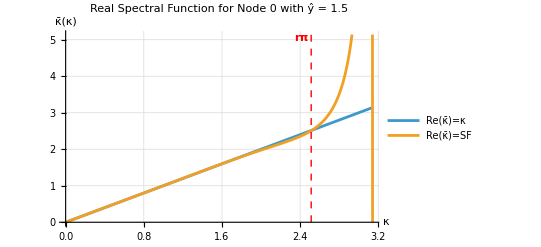

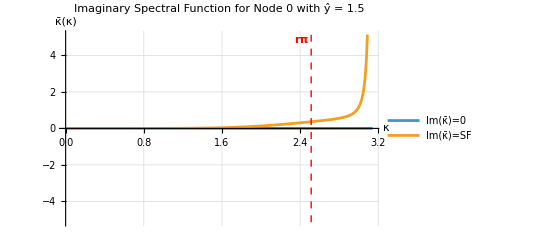

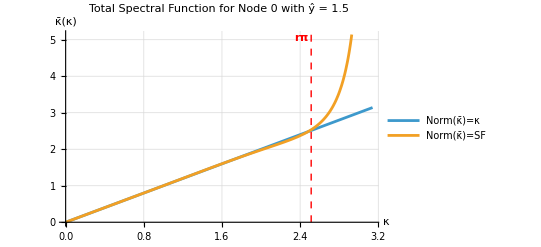

```mathematica
r=0.8;
yHat0List={(*1*)1.50,(*2*)1.59,(*3*)3.12,(*4*)3.27};
yHat=yHat0List[[1]];
Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat2List={(*1*)0.90,(*2*)1.41,(*3*)2.25,(*4*)2.73,(*5*)3.60,(*6*)3.99};
yHat1List={(*1*)0.51,(*2*)1.38,(*3*)1.92,(*4*)2.52,(*5*)3.39};
yHat0List={(*1*)1.50,(*2*)1.59,(*3*)3.12,(*4*)3.27};

yHat2=yHat2List[[1]];
yHat1=yHat1List[[1]];
yHat0=yHat0List[[1]];
```

### Define Coefficients

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsA6/.{a1->a,a2->b,a3->c};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.557322,β→0.0762035,a→0.669438,b→0.225982,c→0.00404124,α12→7.19772,β12→6.12655,α21→0.10995,α22→0.953511,β22→-0.0712249,β31→0.0198292,α31→0.340906,α32→0.774915,β32→0.144777,a1→-3.4454,b1→-5.68769,c1→6.92047,d1→2.83921,e1→-0.815179,f1→0.217445,g1→-0.028852,a2→-0.403072,b2→-1.01572,c2→1.17258,d2→0.337679,e2→-0.109152,f2→0.0197581,g2→-0.00207053,a3→-0.0825683,b3→-0.621588,c3→-0.388584,d3→0.704315,e3→0.375368,f3→0.0135752,g3→-0.000518632}

### Nate Output

```mathematica
interiorNate=interiorCoeffsA6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.557322,β→0.0762035,a1→0.669438,a2→0.225982,a3→0.00404124,γ01→7.19772,γ02→6.12655,γ10→0.10995,γ12→0.953511,γ13→-0.0712249,γ20→0.0198292,γ21→0.340906,γ23→0.774915,γ24→0.144777,a00→-3.4454,a01→-5.68769,a02→6.92047,a03→2.83921,a04→-0.815179,a05→0.217445,a06→-0.028852,a10→-0.403072,a11→-1.01572,a12→1.17258,a13→0.337679,a14→-0.109152,a15→0.0197581,a16→-0.00207053,a20→-0.0825683,a21→-0.621588,a22→-0.388584,a23→0.704315,a24→0.375368,a25→0.0135752,a26→-0.000518632}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2]
```

{γ12Bar→1.34171,γ13Bar→-0.341419,γ21Bar→0.193902,γ23Bar→0.95136,γ24Bar→0.174843,a11Bar→-1.87123,a12Bar→1.9734,a13Bar→0.122279,a14Bar→-0.0935857,a15Bar→-0.0198926,a16Bar→0.00528119,a17Bar→4.79354 (-0.10995 a07+a17),a18Bar→4.79354 (-0.10995 a08+a18),a21Bar→-0.52945,a22Bar→-0.724675,a23Bar→0.777038,a24Bar→0.477097,a25Bar→0.0120911,a26Bar→-0.000175372,a27Bar→10.9839 (-0.0198292 a17+0.10995 a27),a28Bar→10.9839 (-0.0198292 a18+0.10995 a28)}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 1.34171 | -0.341419 | 0 | 0 | 0 | 0 | 0 | 0
0.193902 | 1 | 0.95136 | 0.174843 | 0 | 0 | 0 | 0 | 0
0.0762035 | 0.557322 | 1 | 0.557322 | 0.0762035 | 0 | 0 | 0 | 0
0 | 0.0762035 | 0.557322 | 1 | 0.557322 | 0.0762035 | 0 | 0 | 0
0 | 0 | 0.0762035 | 0.557322 | 1 | 0.557322 | 0.0762035 | 0 | 0
0 | 0 | 0 | 0.0762035 | 0.557322 | 1 | 0.557322 | 0.0762035 | 0
0 | 0 | 0 | 0 | 0.144777 | 0.774915 | 1 | 0.340906 | 0.0198292
0 | 0 | 0 | 0 | 0 | -0.0712249 | 0.953511 | 1 | 0.10995
0 | 0 | 0 | 0 | 0 | 0 | 6.12655 | 7.19772 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | 0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | 0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | 0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-1.87123 | 1.9734 | 0.122279 | -0.0935857 | -0.0198926 | 0.00528119 | 0 | 0 | 0 | 0 | 0
-0.52945 | -0.724675 | 0.777038 | 0.477097 | 0.0120911 | -0.000175372 | 0 | 0 | 0 | 0 | 0
-0.225982 | -0.669438 | 0 | 0.669438 | 0.225982 | 0.00404124 | 0 | 0 | 0 | 0 | 0
-0.00404124 | -0.225982 | -0.669438 | 0 | 0.669438 | 0.225982 | 0.00404124 | 0 | 0 | 0 | 0
0 | -0.00404124 | -0.225982 | -0.669438 | 0 | 0.669438 | 0.225982 | 0.00404124 | 0 | 0 | 0
0 | 0 | -0.00404124 | -0.225982 | -0.669438 | 0 | 0.669438 | 0.225982 | 0.00404124 | 0 | 0
0 | 0 | 0 | -0.00404124 | -0.225982 | -0.669438 | 0 | 0.669438 | 0.225982 | 0.00404124 | 0
0 | 0 | 0 | 0 | -0.00404124 | -0.225982 | -0.669438 | 0 | 0.669438 | 0.225982 | 0.00404124
0 | 0 | 0 | 0 | 0.000518632 | -0.0135752 | -0.375368 | -0.704315 | 0.388584 | 0.621588 | 0.0825683
0 | 0 | 0 | 0 | 0.00207053 | -0.0197581 | 0.109152 | -0.337679 | -1.17258 | 1.01572 | 0.403072
0 | 0 | 0 | 0 | 0.028852 | -0.217445 | 0.815179 | -2.83921 | -6.92047 | 5.68769 | 3.4454)

### Plot Eigenvalue Spectra

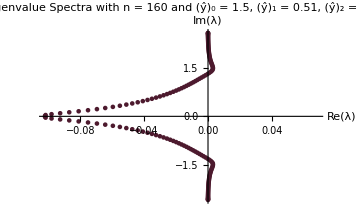

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsA6/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_A6","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP121R3DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.5770460201292381;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.08900836845092142;
		double a1 = 0.6517078440898839;
		double a2 = 0.24815882627035918;
		double a3 = 0.006009630649852392;
		double gamma01 = 9.82050086297005;
		double gamma02 = 10.282867809058313;
		double gamma10 = 0.08185064221829087;
		double gamma12 = 1.6890627481714804;
		double gamma13 = 0.4961478931388701;
		double gamma20 = 0.017918887158094664;
		double gamma21 = 0.33500390219730425;
		double gamma23 = 0.7548768581531722;
		double gamma24 = 0.13667343083285768;
		double a00 =  - 3.73445251380582;
		double a01 =  - 10.765902315893966;
		double a02 = 11.158777481815811;
		double a03 = 3.8932795799881186;
		double a04 =  - 0.6389839738157034;
		double a05 = 0.09587727397420936;
		double a06 =  - 0.008595531676508965;
		double a10 =  - 0.31850909623427476;
		double a11 =  - 1.396944235854646;
		double a12 = 0.5364016058704685;
		double a13 = 1.1223168928950014;
		double a14 = 0.059450604503400145;
		double a15 =  - 0.0027438380250710795;
		double a16 = 0.00002806684476978311;
		double a20 =  - 0.07670359108573083;
		double a21 =  - 0.6273443641711278;
		double a22 =  - 0.37833992259630045;
		double a23 = 0.7128462614236629;
		double a24 = 0.3572245284141374;
		double a25 = 0.012842138314361781;
		double a26 =  - 0.0005250502990408262;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06},
			{a10, a11, a12, a13, a14, a15, a16},
			{a20, a21, a22, a23, a24, a25, a26}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a3, -a2, -a1, 0.0, a1, a2, a3
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_P4_yHat0_1.89_yHat1_1.65_yHat2_1.14.h

# P6 (B6) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0
0
0 γ_01
1
γ_21
γ_31
0
0
0
0
0 γ_02
γ_12
1
γ_32
β
0
0
0
0 0
γ_13
γ_23
1
α
γ_35
0
0
0 0
0
γ_24
γ_34
1
γ_34
γ_24
0
0 0
0
0
γ_35
α
1
γ_23
γ_13
0 0
0
0
0
β
γ_32
1
γ_12
γ_02 0
0
0
0
0
γ_31
γ_21
1
γ_01 0
0
0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
a_30
-a_4
-a_38
-a_28
-a_18
-a_08 a_01
a_11
a_21
a_31
-a_3
-a_37
-a_27
-a_17
-a_07 a_02
a_12
a_22
a_32
-a_2
-a_36
-a_26
-a_16
-a_06 a_03
a_13
a_23
a_33
-a_1
-a_35
-a_25
-a_15
-a_05 a_04
a_14
a_24
a_34
0
-a_34
-a_24
-a_14
-a_04 a_05
a_15
a_25
a_35
a_1
-a_33
-a_23
-a_13
-a_03 a_06
a_16
a_26
a_36
a_2
-a_32
-a_22
-a_12
-a_02 a_07
a_17
a_27
a_37
a_3
-a_31
-a_21
-a_11
-a_01 a_08
a_18
a_28
a_38
a_4
-a_30
-a_20
-a_10
-a_00 )

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
(*Note that these are found with the P6 Scheme NEW header in that notebook*)
interiorCoeffsP6={α->0.59067138684056,β->0.10005088370852962,a1->0.6375976953896195,a2->0.26328410014665704,a3->0.009340368066539819,a4->-0.0003661823333658686};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["P6_bdCoeffs3.mx"];
Get["P6_bdCoeffs2.mx"];
Get["P6_bdCoeffs1.mx"];
Get["P6_bdCoeffs0.mx"];
```

## General Extrapolation Polynomial

For the P6 (B6) scheme, we have:
	LHSBandCount = 5
	n = 6
	freeInteriorPars = 3
	yDeriv = 14

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=3; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=14; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192 | 16384 | 32768 | 65536
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323 | 4782969 | 14348907 | 43046721
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864 | 268435456 | 1073741824 | 4294967296
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125 | 6103515625 | 30517578125 | 152587890625
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016 | 78364164096 | 470184984576 | 2821109907456
1 | 7 | 49 | 343 | 2401 | 16807 | 117649 | 823543 | 5764801 | 40353607 | 282475249 | 1977326743 | 13841287201 | 96889010407 | 678223072849 | 4747561509943 | 33232930569601
1 | 8 | 64 | 512 | 4096 | 32768 | 262144 | 2097152 | 16777216 | 134217728 | 1073741824 | 8589934592 | 68719476736 | 549755813888 | 4398046511104 | 35184372088832 | 281474976710656
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576 | 53248 | 114688 | 245760 | 524288
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764 | 6908733 | 22320522 | 71744535 | 229582512
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648 | 218103808 | 939524096 | 4026531840 | 17179869184
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500 | 3173828125 | 17089843750 | 91552734375 | 488281250000
0 | 1 | 12 | 108 | 864 | 6480 | 46656 | 326592 | 2239488 | 15116544 | 100776960 | 665127936 | 4353564672 | 28298170368 | 182849716224 | 1175462461440 | 7522959753216
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 87178291200 | 1307674368000 yHat | 10461394944000 yHat^2) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13
p14
p15
p16) = (f0
f1
f2
f3
f4
f5
f6
f7
f8
fp0
fp1
fp2
fp3
fp4
fp5
fp6
0)

Singularities:
(yHat→2.94357
yHat→4.18143)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList3 in terms of the optimization free parameter ŷ
Variables:
	fVars3: List of f_i and f_i' variables that will appear in the shifted stencil for Node 3
	bdCoeffsList3: List of boundary coefficients that will appear in the shifted stencil for Node 3
	schemeShifted: The shifted scheme for Node 3
	schemeCentered: The centered scheme for Node 3 in terms of the extrapolation polynomial P(x)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode4: The scheme for Node 4, which only depends on interiorCoeffsP6
	SOLfp6: The solution to Node 4’s scheme equation for f_6' in terms of fVars3
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs3: System of equations with each of the coefficient terms equal to each other
	bdCoeffs3: Solution to the system of equations for bdCoeffsList3 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars3 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars3 as well as f_6'. We eliminate the dependence on f_6' by using Node 4’s scheme to solve for f_6' in terms of fVars3.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars3, we construct a system of equations by equating the coefficient in front of each term of fVars3 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList3 in terms of interiorCoeffsP6 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_33=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_33 so that bdCoeffsList3 and fVars3 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs3 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Nodes 2, 1, and 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 4 for f_6' in terms of the other fVars, we must also do the same for f_5' (Nodes 2, 1, and 0), f_4' (Nodes 1 and 0), and f_3' (Node 0) using Nodes 3, 2, and 1, respectively.

### Node 3

```mathematica
(*----------STEP 1----------*)
fVars3={fp1,fp2,fp3,fp4,fp5,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList3={γ31,γ32,γ33,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38};
schemeShifted=γ31 fp1+γ32 fp2+γ33 fp3+γ34 fp4+γ35 fp5-(a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8); (*==0*)
schemeCentered=β fp1+α fp2+fp3+α fp4+β fp5-(-a4 P[-1]-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6+a4 f7); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fp2+α fp3+fp4+α fp5+β fp6==-a4 f0-a3 f1-a2 f2-a1 f3+a1 f5+a2 f6+a3 f7+a4 f8;
SOLfp6=Solve[schemeNode4,fp6][[1,1]]/.interiorCoeffsP6;
schemeCentered=schemeCentered/.SOLfp6;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars3];

(*----------STEP 4----------*)
coeffEqs3=Table[Coefficient[eq,fVars3[[i]]]==0,{i,1,Length@fVars3}];
bdCoeffs3=(Solve[coeffEqs3,bdCoeffsList3][[1]])/.interiorCoeffsP6;

(*----------STEP 5----------*)
(*DumpSave["P6_bdCoeffs3.mx","Global`bdCoeffs3"];*)
```

### Node 2

```mathematica
(*----------STEP 1----------*)
fVars2={fp0,fp1,fp2,fp3,fp4,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28};
schemeShifted=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8); (*==0*)
schemeCentered=β fp0+α fp1+fp2+α fp3+β fp4-(-a4 P[-2]-a3 P[-1]-a2 f0-a1 f1+a1 f3+a2 f4+a3 f5+a4 f6); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fp2+α fp3+fp4+α fp5+β fp6==-a4 f0-a3 f1-a2 f2-a1 f3+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fp1+γ32 fp2+γ33 fp3+γ34 fp4+γ35 fp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
SOLfp6=Solve[schemeNode4,fp6][[1,1]]/.interiorCoeffsP6;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.bdCoeffs3;
schemeCentered=schemeCentered/.SOLfp6/.SOLfp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsP6;

(*----------STEP 5----------*)
DumpSave["P6_bdCoeffs2.mx","Global`bdCoeffs2"];
```

### Node 1

```mathematica
(*----------STEP 1----------*)
fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18};
schemeShifted=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6+a17 f7+a18 f8); (*==0*)
schemeCentered=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a4 P[-3]-a3 P[-2]-a2 P[-1]-a1 f0+a1 f2+a2 f3+a3 f4+a4 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fp2+α fp3+fp4+α fp5+β fp6==-a4 f0-a3 f1-a2 f2-a1 f3+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fp1+γ32 fp2+γ33 fp3+γ34 fp4+γ35 fp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8;
SOLfp6=Solve[schemeNode4,fp6][[1,1]]/.interiorCoeffsP6;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.bdCoeffs3;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfp6/.SOLfp5/.SOLfp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsP6;

(*----------STEP 5----------*)
DumpSave["P6_bdCoeffs1.mx","Global`bdCoeffs1"];
```

### Node 0

```mathematica
(*----------STEP 1----------*)
fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08};
schemeShifted=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6+a07 f7+a08 f8); (*==0*)
schemeCentered=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a4 P[-4]-a3 P[-3]-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2+a3 f3+a4 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fp2+α fp3+fp4+α fp5+β fp6==-a4 f0-a3 f1-a2 f2-a1 f3+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fp1+γ32 fp2+γ33 fp3+γ34 fp4+γ35 fp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8;
schemeNode1=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6+a17 f7+a18 f8;
SOLfp6=Solve[schemeNode4,fp6][[1,1]]/.interiorCoeffsP6;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.bdCoeffs3;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
SOLfp3=Solve[schemeNode1,fp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfp6/.SOLfp5/.SOLfp4/.SOLfp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsP6;

(*----------STEP 5----------*)
DumpSave["P6_bdCoeffs0.mx","Global`bdCoeffs0"];
```

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38]
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08]

{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}=1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3;
{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0;
```

### Node 3

```mathematica
𝔸3[κ_]=γ31 Cos[κ]+γ32 Cos[2 κ]+Cos[3 κ]+γ34 Cos[4 κ]+γ35 Cos[5 κ];
𝔹3[κ_]=γ31 Sin[κ]+γ32 Sin[2 κ]+Sin[3 κ]+γ34 Sin[4 κ]+γ35 Sin[5 κ];
ℂ3[κ_]=a30+a31 Cos[κ]+a32 Cos[2 κ]+a33 Cos[3 κ]+a34 Cos[4 κ]+a35 Cos[5 κ]+a36 Cos[6 κ]+a37 Cos[7 κ]+a38 Cos[8 κ];
𝔻3[κ_]=a31 Sin[κ]+a32 Sin[2 κ]+a33 Sin[3 κ]+a34 Sin[4 κ]+a35 Sin[5 κ]+a36 Sin[6 κ]+a37 Sin[7 κ]+a38 Sin[8 κ];
κBar3Re[κ_]=(𝔸3[κ]*𝔻3[κ]-𝔹3[κ]*ℂ3[κ])/((𝔸3[κ])^2+(𝔹3[κ])^2);
κBar3Im[κ_]=(-𝔸3[κ]*ℂ3[κ]-𝔹3[κ]*𝔻3[κ])/((𝔸3[κ])^2+(𝔹3[κ])^2);
κBar3Norm[κ_]=Abs[κBar3Re[κ]+I*κBar3Im[κ]];
```

```mathematica
Δ3Re[κ_]=(κ*((𝔸3[κ])^2+(𝔹3[κ])^2)-(𝔸3[κ]*𝔻3[κ]-𝔹3[κ]*ℂ3[κ]))^2;
Δ3Im[κ_]=(0*((𝔸3[κ])^2+(𝔹3[κ])^2)-(-𝔸3[κ]*ℂ3[κ]-𝔹3[κ]*𝔻3[κ]))^2;
Δ3Norm[κ_]=(κ-κBar3Norm[κ])^2;
```

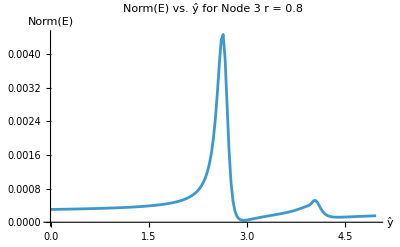

Evaluation time: 18.067083

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat3Array=Range[0,5,0.03];
Δ3NormArray=Table[Δ3Norm[κ]/.{yHat->yHat3Array[[i]]},{i,1,Length@yHat3Array}];
ENorm3Array=Table[NIntegrate[Δ3NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat3Array}];

ListPlot[Transpose@{yHat3Array,ENorm3Array},Joined->True,PlotRange->All,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 3\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ]+a27 Cos[7 κ]+a28 Cos[8 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ]+a27 Sin[7 κ]+a28 Sin[8 κ];
κBar2Re[κ_]=(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ-κBar2Norm[κ])^2;
```

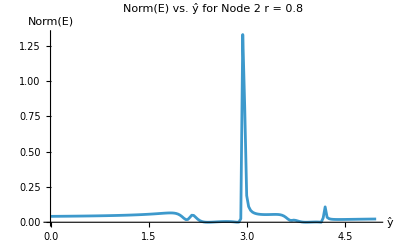

Evaluation time: 18.089397

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotRange->All,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ]+a17 Cos[7 κ]+a18 Cos[8 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ]+a17 Sin[7 κ]+a18 Sin[8 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

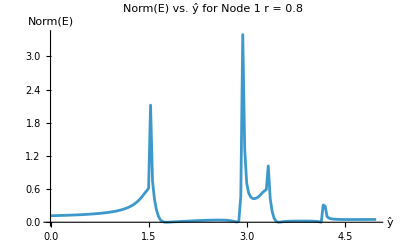

Evaluation time: 35.066831

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotRange->All,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ]+a07 Cos[7 κ]+a08 Cos[8 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ]+a07 Sin[7 κ]+a08 Sin[8 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

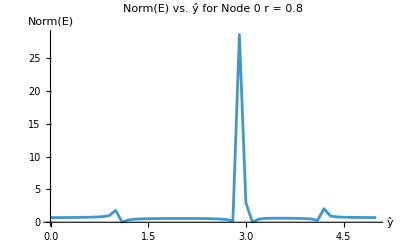

Evaluation time: 138.323874

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.1];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotRange->All,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 3

```mathematica
Clear[yHat]
SF3Re[κ_,yHat_]=κBar3Re[κ];
SF3Im[κ_,yHat_]=κBar3Im[κ];
SF3Norm[κ_,yHat_]=κBar3Norm[κ];
```

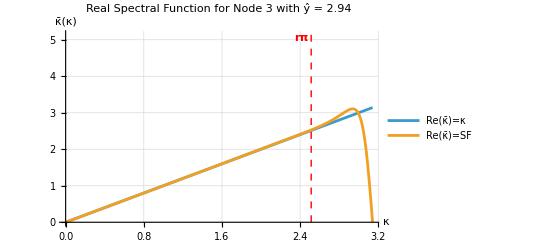

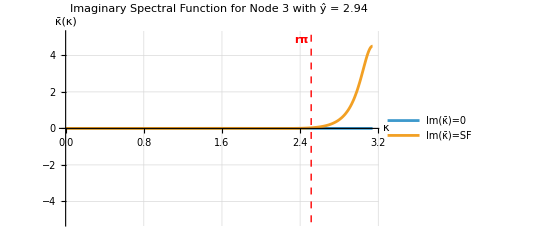

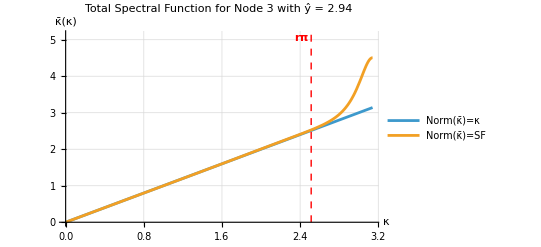

```mathematica
r=0.8;
yHat3List={(*1*)2.94,(*2*)4.41};
yHat=yHat3List[[1]];
Plot[{κ,SF3Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF3Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF3Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

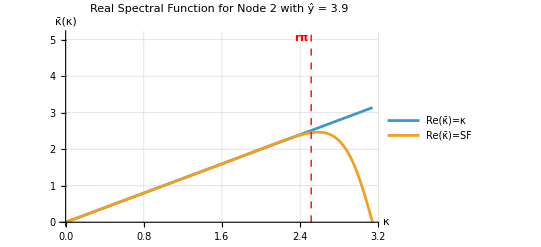

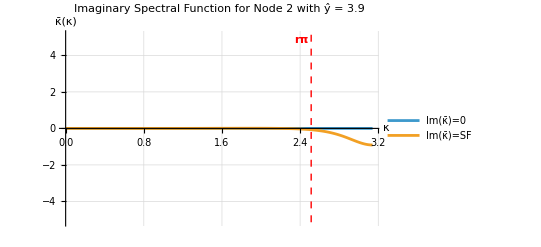

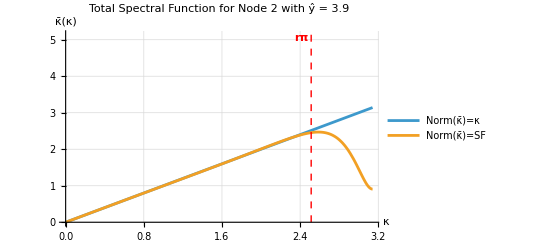

```mathematica
r=0.8;
yHat2List={(*1*)2.07,(*2*)2.85,(*3*)3.90,(*4*)4.14};
yHat=yHat2List[[3]];
Plot[{κ,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

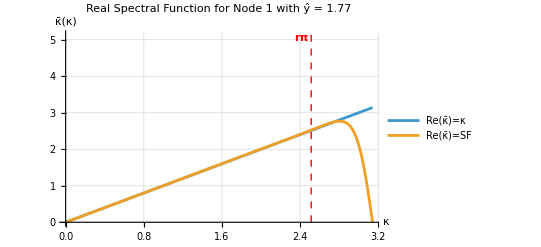

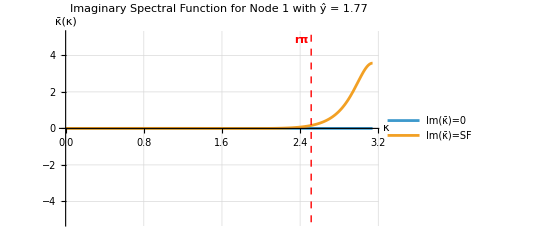

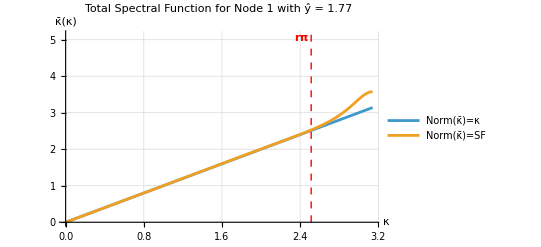

```mathematica
r=0.8;
yHat1List={(*1*)1.77,(*2*)2.85,(*3*)3.48,(*4*)4.14};
yHat=yHat1List[[1]];
Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

```mathematica
r=0.8;
yHat0List={(*1*)1.1,(*2*)2.8,(*3*)3.1,(*4*)4.1};
yHat=yHat0List[[1]];
Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

$Aborted

$Aborted

$Aborted

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat3,yHat2,yHat1,yHat0]

yHat3List={(*1*)2.94,(*2*)4.41};
yHat2List={(*1*)2.07,(*2*)2.85,(*3*)3.90,(*4*)4.14};
yHat1List={(*1*)1.77,(*2*)2.85,(*3*)3.48,(*4*)4.14};
yHat0List={(*1*)1.1,(*2*)2.8,(*3*)3.1,(*4*)4.1};

yHat0=yHat0List[[1]];
yHat2=yHat2List[[2]];
yHat1=yHat1List[[1]];
yHat3=yHat3List[[2]];
```

### Define Coefficients

```mathematica
Clear[γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38]
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08]

{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsP6/.{a1->a,a2->b,a3->c,a4->d};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,β41->γ31val,α41->γ32val,α42->γ34val,β42->γ35val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,h1->a07val,i1->a08val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,h2->a17val,i2->a18val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val,h3->a27val,i3->a28val,a4->a30val,b4->a31val,c4->a32val,d4->a33val,e4->a34val,f4->a35val,g4->a36val,h4->a37val,i4->a38val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.590671,β→0.100051,a→0.637598,b→0.263284,c→0.00934037,d→-0.000366182,α12→114.339,β12→144.896,α21→0.0635983,α22→2.82014,β22→1.60377,β31→0.0119367,α31→0.265683,α32→1.06787,β32→0.299099,β41→0.0702506,α41→0.464554,α42→0.752869,β42→0.160931,a1→-39.499,b1→-142.518,c1→122.754,d1→73.8178,e1→-18.7505,f1→5.29544,g1→-1.33358,h1→0.264065,i1→-0.0297841,a2→-0.231725,b2→-1.85059,c2→-0.737401,d2→2.42428,e2→0.455903,f2→-0.0715549,g2→0.0127828,h2→-0.00184243,i2→0.00014704,a3→-0.0558354,b3→-0.54093,c3→-0.673487,d3→0.588162,e3→0.637429,f3→0.0491551,g3→-0.00508825,h3→0.000652478,i3→-0.0000581082,a4→-0.010119,b4→-0.179084,c4→-0.601477,d4→-0.249031,e4→0.636135,f4→0.38494,g4→0.0199015,h4→-0.001341,i4→0.0000757937}

### Nate Output

```mathematica
interiorNate=interiorCoeffsP6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.590671,β→0.100051,a1→0.637598,a2→0.263284,a3→0.00934037,a4→-0.000366182,γ01→114.339,γ02→144.896,γ10→0.0635983,γ12→2.82014,γ13→1.60377,γ20→0.0119367,γ21→0.265683,γ23→1.06787,γ24→0.299099,γ31→0.0702506,γ32→0.464554,γ34→0.752869,γ35→0.160931,a00→-39.499,a01→-142.518,a02→122.754,a03→73.8178,a04→-18.7505,a05→5.29544,a06→-1.33358,a07→0.264065,a08→-0.0297841,a10→-0.231725,a11→-1.85059,a12→-0.737401,a13→2.42428,a14→0.455903,a15→-0.0715549,a16→0.0127828,a17→-0.00184243,a18→0.00014704,a20→-0.0558354,a21→-0.54093,a22→-0.673487,a23→0.588162,a24→0.637429,a25→0.0491551,a26→-0.00508825,a27→0.000652478,a28→-0.0000581082,a30→-0.010119,a31→-0.179084,a32→-0.601477,a33→-0.249031,a34→0.636135,a35→0.38494,a36→0.0199015,a37→-0.001341,a38→0.0000757937}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3]
```

{γ12Bar→1.01965,γ13Bar→-0.255715,γ21Bar→0.1657,γ23Bar→1.62923,γ24Bar→0.635449,γ31Bar→0.0702506,γ32Bar→0.464554,γ34Bar→0.752869,γ35Bar→0.160931,a11Bar→-1.15013,a12Bar→1.36236,a13Bar→0.362006,a14Bar→-0.262831,a15Bar→0.0651073,a16Bar→-0.0155613,a17Bar→0.00297151,a18Bar→-0.000325469,a21Bar→-0.411299,a22Bar→-1.13681,a23Bar→0.282884,a24Bar→1.17245,a25Bar→0.132965,a26Bar→-0.0159074,a27Bar→0.0021209,a28Bar→-0.000182086,a31Bar→-0.179084,a32Bar→-0.601477,a33Bar→-0.249031,a34Bar→0.636135,a35Bar→0.38494,a36Bar→0.0199015,a37Bar→-0.001341,a38Bar→0.0000757937}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=4;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==3&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==5),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
γ31Bar | γ32Bar | 1 | γ34Bar | γ35Bar | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | γ35 | γ34 | 1 | γ32 | γ31 | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 1.01965 | -0.255715 | 0 | 0 | 0 | 0 | 0 | 0
0.1657 | 1 | 1.62923 | 0.635449 | 0 | 0 | 0 | 0 | 0
0.0702506 | 0.464554 | 1 | 0.752869 | 0.160931 | 0 | 0 | 0 | 0
0 | 0.100051 | 0.590671 | 1 | 0.590671 | 0.100051 | 0 | 0 | 0
0 | 0 | 0.100051 | 0.590671 | 1 | 0.590671 | 0.100051 | 0 | 0
0 | 0 | 0 | 0.160931 | 0.752869 | 1 | 0.464554 | 0.0702506 | 0
0 | 0 | 0 | 0 | 0.299099 | 1.06787 | 1 | 0.265683 | 0.0119367
0 | 0 | 0 | 0 | 0 | 1.60377 | 2.82014 | 1 | 0.0635983
0 | 0 | 0 | 0 | 0 | 0 | 144.896 | 114.339 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==1&&j==7),a17Bar,
If[(i==1&&j==8),a18Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,
If[(i==2&&j==7),a27Bar,
If[(i==2&&j==8),a28Bar,

If[(i==3&&j==1),a31Bar,
If[(i==3&&j==2),a32Bar,
If[(i==3&&j==3),a33Bar,
If[(i==3&&j==4),a34Bar,
If[(i==3&&j==5),a35Bar,
If[(i==3&&j==6),a36Bar,
If[(i==3&&j==7),a37Bar,
If[(i==3&&j==8),a38Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k&&j==k-7),-a07,
If[(i==k&&j==k-8),-a08,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-1&&j==k-7),-a17,
If[(i==k-1&&j==k-8),-a18,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,
If[(i==k-2&&j==k-7),-a27,
If[(i==k-2&&j==k-8),-a28,
If[(i==k-3&&j==k),-a30,
If[(i==k-3&&j==k-1),-a31,
If[(i==k-3&&j==k-2),-a32,
If[(i==k-3&&j==k-3),-a33,
If[(i==k-3&&j==k-4),-a34,
If[(i==k-3&&j==k-5),-a35,
If[(i==k-3&&j==k-6),-a36,
If[(i==k-3&&j==k-7),-a37,
If[(i==k-3&&j==k-8),-a38,


If[i-4==j,-a4,
If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
If[i+4==j,a4,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | a17Bar | a18Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | a27Bar | a28Bar | 0 | 0 | 0
a31Bar | a32Bar | a33Bar | a34Bar | a35Bar | a36Bar | a37Bar | a38Bar | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | a4 | 0 | 0 | 0
-a4 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | a4 | 0 | 0
0 | -a4 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | a4 | 0
0 | 0 | -a4 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | a4
0 | 0 | -a38 | -a37 | -a36 | -a35 | -a34 | -a33 | -a32 | -a31 | -a30
0 | 0 | -a28 | -a27 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | -a18 | -a17 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | -a08 | -a07 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-1.15013 | 1.36236 | 0.362006 | -0.262831 | 0.0651073 | -0.0155613 | 0.00297151 | -0.000325469 | 0 | 0 | 0
-0.411299 | -1.13681 | 0.282884 | 1.17245 | 0.132965 | -0.0159074 | 0.0021209 | -0.000182086 | 0 | 0 | 0
-0.179084 | -0.601477 | -0.249031 | 0.636135 | 0.38494 | 0.0199015 | -0.001341 | 0.0000757937 | 0 | 0 | 0
-0.00934037 | -0.263284 | -0.637598 | 0 | 0.637598 | 0.263284 | 0.00934037 | -0.000366182 | 0 | 0 | 0
0.000366182 | -0.00934037 | -0.263284 | -0.637598 | 0 | 0.637598 | 0.263284 | 0.00934037 | -0.000366182 | 0 | 0
0 | 0.000366182 | -0.00934037 | -0.263284 | -0.637598 | 0 | 0.637598 | 0.263284 | 0.00934037 | -0.000366182 | 0
0 | 0 | 0.000366182 | -0.00934037 | -0.263284 | -0.637598 | 0 | 0.637598 | 0.263284 | 0.00934037 | -0.000366182
0 | 0 | -0.0000757937 | 0.001341 | -0.0199015 | -0.38494 | -0.636135 | 0.249031 | 0.601477 | 0.179084 | 0.010119
0 | 0 | 0.0000581082 | -0.000652478 | 0.00508825 | -0.0491551 | -0.637429 | -0.588162 | 0.673487 | 0.54093 | 0.0558354
0 | 0 | -0.00014704 | 0.00184243 | -0.0127828 | 0.0715549 | -0.455903 | -2.42428 | 0.737401 | 1.85059 | 0.231725
0 | 0 | 0.0297841 | -0.264065 | 1.33358 | -5.29544 | 18.7505 | -73.8178 | -122.754 | 142.518 | 39.499)

### Plot Eigenvalue Spectra

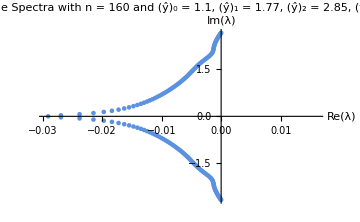

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsP6/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,β41->gamma31,α41->gamma32,α42->gamma34,β42->gamma35,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,h1->a07,i1->a08,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,h2->a17,i2->a18,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26,h3->a27,i3->a28,a4->a30,b4->a31,c4->a32,d4->a33,e4->a34,f4->a35,g4->a36,h4->a37,i4->a38};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24,gamma31,gamma32,gamma34,gamma35};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a07,a08,a10,a11,a12,a13,a14,a15,a16,a17,a18,a20,a21,a22,a23,a24,a25,a26,a27,a28,a30,a31,a32,a33,a34,a35,a36,a37,a38};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_P6","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],"_yHat3_",ToString[yHat3],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP6R4DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.59067138684056;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.10005088370852962;
		double a1 = 0.6375976953896195;
		double a2 = 0.26328410014665704;
		double a3 = 0.009340368066539819;
		double a4 =  - 0.0003661823333658686;
		double gamma01 = 1.9429265968126401;
		double gamma02 = 2.4621754563022478;
		double gamma10 =  - 0.11667782650556546;
		double gamma12 =  - 17.193865340181674;
		double gamma13 =  - 9.39872085284378;
		double gamma20 = 0.20719757825417595;
		double gamma21 = 5.509156946224238;
		double gamma23 = 32.9663351127424;
		double gamma24 = 10.370454614959954;
		double gamma31 =  - 1.412205637381021;
		double gamma32 =  - 12.179494791248999;
		double gamma34 =  - 22.605979156927333;
		double gamma35 =  - 4.717823329386192;
		double a00 =  - 0.6711965370977566;
		double a01 =  - 2.421779258314018;
		double a02 = 2.0859266290726737;
		double a03 = 1.2543682073520586;
		double a04 =  - 0.31862314280448345;
		double a05 = 0.08998417189866359;
		double a06 =  - 0.022661156448407382;
		double a07 = 0.004487199819524612;
		double a08 =  - 0.0005061136154759227;
		double a10 = 1.53741941875424;
		double a11 = 11.47953998576969;
		double a12 = 3.8008470975778437;
		double a13 =  - 14.58490089913063;
		double a14 =  - 2.5556001658142122;
		double a15 = 0.37604524502211234;
		double a16 =  - 0.059969678023698236;
		double a17 = 0.0069917829624128736;
		double a18 =  - 0.0003727870949550155;
		double a20 =  - 0.9347303475345967;
		double a21 =  - 12.627080075062452;
		double a22 =  - 22.679232689047012;
		double a23 = 13.400628101848667;
		double a24 = 21.211257893886796;
		double a25 = 1.7860848769078075;
		double a26 =  - 0.17403439487614847;
		double a27 = 0.018333978323435862;
		double a28 =  - 0.0012273444489978337;
		double a30 = 0.13359381233000178;
		double a31 = 4.138924951595243;
		double a32 = 17.88103301327942;
		double a33 = 9.05327613445678;
		double a34 =  - 19.2179998786429;
		double a35 =  - 11.464399787180412;
		double a36 =  - 0.5586519666134571;
		double a37 = 0.036240008477330776;
		double a38 =  - 0.002016287701435117;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24},
			{0.0, gamma31, gamma32, 1.0, gamma34, gamma35}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06, a07, a08},
			{a10, a11, a12, a13, a14, a15, a16, a17, a18},
			{a20, a21, a22, a23, a24, a25, a26, a27, a28},
			{a30, a31, a32, a33, a34, a35, a36, a37, a38}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a4, -a3, -a2, -a1, 0.0, a1, a2, a3, a4
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_P6_yHat0_1.1_yHat1_1.8_yHat2_2.4_yHat3_2.9.h

# P6 (C6) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
β
0
0 γ_01
1
α
γ_13
0 γ_02
γ_12
1
γ_12
γ_02 0
γ_13
α
1
γ_01 0
0
β
γ_10
1)
	Q=(a_00
a_01
-a_2
-a_14
-a_04 a_01
a_11
-a_1
-a_13
-a_03 a_02
a_12
0
-a_12
-a_02 a_03
a_13
a_1
-a_11
-a_01 a_04
a_14
a_2
-a_10
-a_00)

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
(*interiorCoeffsC6={α->0.4963477370017426,β->0.04075360091710232,a1->0.723439643221641,a2->0.15683084734860173};*)
Get["C6_interiorCoeffs.mx"]

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["C6_bdCoeffs1.mx"];
Get["C6_bdCoeffs0.mx"];
```

## General Extrapolation Polynomial

For the P6 (C6) scheme, we have:
	LHSBandCount = 5
	n = 6
	freeInteriorPars = 1
	yDeriv = 6

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=1; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=6; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440
0 | 0 | 0 | 0 | 0 | 0 | 720 | 5040 yHat | 20160 yHat^2 | 60480 yHat^3 | 151200 yHat^4) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10) = (f0
f1
f2
f3
f4
fp0
fp1
fp2
fp3
fp4
0)

Singularities:
(yHat→1.63853
yHat→2.36147
yHat→0.903336
yHat→3.09666)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList1 in terms of the optimization free parameter ŷ
Variables:
	fVars1: List of f_i and f_i' variables that will appear in the shifted stencil for Node 1
	bdCoeffsList1: List of boundary coefficients that will appear in the shifted stencil for Node 1
	schemeShifted: The shifted scheme for Node 1
	schemeCentered: The centered scheme for Node 1 in terms of the extrapolation polynomial P(x)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode2: The scheme for Node 2, which only depends on interiorCoeffsC6
	SOLfp4: The solution to Node 2’s scheme equation for f_4' in terms of fVars1
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs1: System of equations with each of the coefficient terms equal to each other
	bdCoeffs1: Solution to the system of equations for bdCoeffsList1 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars1 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars1 as well as f_4'. We eliminate the dependence on f_4' by using Node 2’s scheme to solve for f_4' in terms of fVars1.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars1, we construct a system of equations by equating the coefficient in front of each term of fVars1 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList1 in terms of interiorCoeffsC6 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_11=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_11 so that bdCoeffsList1 and fVars1 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs1 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 2 for f_4' in terms of the other fVars, we must also do the same for f_3' using Node.

### Node 1

```mathematica
(*----------STEP 1----------*)
fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14};
schemeShifted=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4); (*==0*)
schemeCentered=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a2 P[-1]-a1 f0+a1 f2+a2 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode2=β fp0+α fp1+fp2+α fp3+β fp4==-a2 f0-a1 f1+a1 f3+a2 f4;

SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.interiorCoeffsC6;
schemeCentered=schemeCentered/.SOLfp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsC6;

(*----------STEP 5----------*)
(*DumpSave["C6_bdCoeffs1.mx","Global`bdCoeffs1"]*)
```

### Node 0

```mathematica
(*----------STEP 1----------*)
fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04};
schemeShifted=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4); (*==0*)
schemeCentered=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2); (*==0*)

(*----------STEP 2----------*)
schemeNode2=β fp0+α fp1+fp2+α fp3+β fp4==-a2 f0-a1 f1+a1 f3+a2 f4;
schemeNode1=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4;

SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.interiorCoeffsC6;
SOLfp3=Solve[schemeNode1,fp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfp4/.SOLfp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsC6;

(*----------STEP 5----------*)
(*DumpSave["C6_bdCoeffs0.mx","Global`bdCoeffs0"]*)
```

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04]

{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0;
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

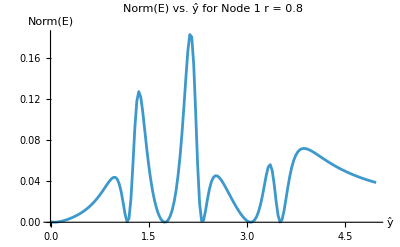

Evaluation time: 7.9797865

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

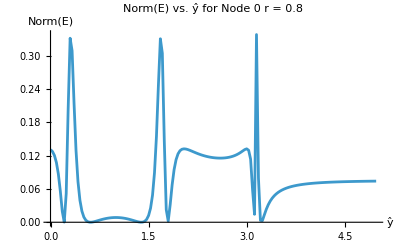

Evaluation time: 13.983051

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

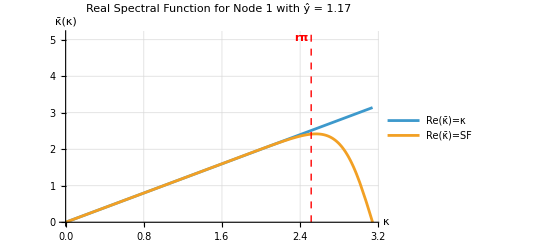

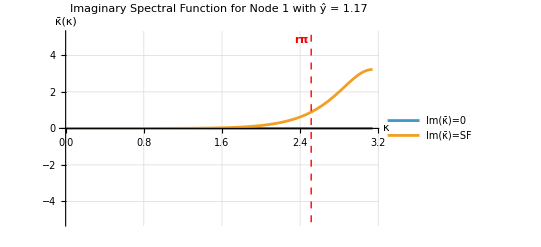

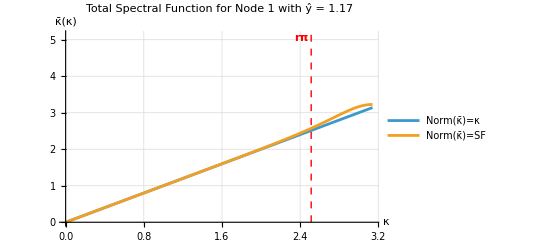

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)1.17,(*2*)1.74,(*3*)2.31,(*4*)3.06,(*5*)3.51};
yHat=yHat1List[[1]];
Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

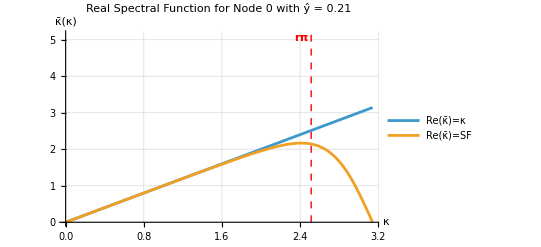

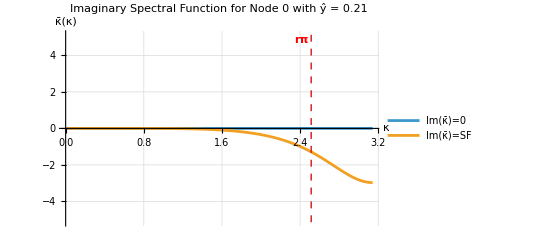

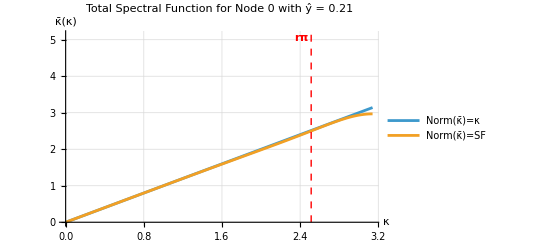

```mathematica
r=0.8;
yHat0List={(*1*)0.21,(*2*)0.60,(*3*)1.38,(*4*)1.80,(*5*)3.12,(*6*)3.24};
yHat=yHat0List[[1]];
Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat1,yHat0]

yHat1List={(*1*)1.17,(*2*)1.74,(*3*)2.31,(*4*)3.06,(*5*)3.51};
yHat0List={(*1*)0.21,(*2*)0.60,(*3*)1.38,(*4*)1.80,(*5*)3.12,(*6*)3.24};

yHat1=yHat1List[[1]];
yHat0=yHat0List[[1]];
```

### Define Coefficients

```mathematica
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04]

{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsC6/.{a1->a,a2->b};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.496348,β→0.0407536,a→0.72344,b→0.156831,α12→-3.53134,β12→-11.297,α21→0.161231,α22→0.474149,β22→-0.0389784,a1→-2.14192,b1→14.4741,c1→-8.29701,d1→-4.43234,e1→0.397139,a2→-0.543136,b2→-0.524,c2→1.07478,d2→-0.00140849,e2→-0.00623134}

### Nate Output

```mathematica
interiorNate=interiorCoeffsC6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.496348,β→0.0407536,a1→0.72344,a2→0.156831,γ01→-3.53134,γ02→-11.297,γ10→0.161231,γ12→0.474149,γ13→-0.0389784,a00→-2.14192,a01→14.4741,a02→-8.29701,a03→-4.43234,a04→0.397139,a10→-0.543136,a11→-0.524,a12→1.07478,a13→-0.00140849,a14→-0.00623134}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1]
```

{γ12Bar→1.46274,γ13Bar→-0.0248372,a11Bar→-1.82091,a12Bar→1.53726,a13Bar→0.454465,a14Bar→-0.0447713}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
α | 1 | α | β | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 1.46274 | -0.0248372 | 0 | 0 | 0 | 0 | 0 | 0
0.496348 | 1 | 0.496348 | 0.0407536 | 0 | 0 | 0 | 0 | 0
0.0407536 | 0.496348 | 1 | 0.496348 | 0.0407536 | 0 | 0 | 0 | 0
0 | 0.0407536 | 0.496348 | 1 | 0.496348 | 0.0407536 | 0 | 0 | 0
0 | 0 | 0.0407536 | 0.496348 | 1 | 0.496348 | 0.0407536 | 0 | 0
0 | 0 | 0 | 0.0407536 | 0.496348 | 1 | 0.496348 | 0.0407536 | 0
0 | 0 | 0 | 0 | 0.0407536 | 0.496348 | 1 | 0.496348 | 0.0407536
0 | 0 | 0 | 0 | 0 | -0.0389784 | 0.474149 | 1 | 0.161231
0 | 0 | 0 | 0 | 0 | 0 | -11.297 | -3.53134 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,


If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
0]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | 0 | 0 | 0 | 0 | 0 | 0 | 0
-a1 | 0 | a1 | a2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -a2 | -a1 | 0 | a1 | a2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -a2 | -a1 | 0 | a1 | a2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -a2 | -a1 | 0 | a1 | a2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -a2 | -a1 | 0 | a1 | a2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -a2 | -a1 | 0 | a1 | a2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a2 | -a1 | 0 | a1 | a2
0 | 0 | 0 | 0 | 0 | 0 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | 0 | 0 | 0 | 0 | -a04 | -a03 | -a02 | -a01 | -a00)

(-1.82091 | 1.53726 | 0.454465 | -0.0447713 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.72344 | 0 | 0.72344 | 0.156831 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.156831 | -0.72344 | 0 | 0.72344 | 0.156831 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.156831 | -0.72344 | 0 | 0.72344 | 0.156831 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.156831 | -0.72344 | 0 | 0.72344 | 0.156831 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.156831 | -0.72344 | 0 | 0.72344 | 0.156831 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.156831 | -0.72344 | 0 | 0.72344 | 0.156831 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.156831 | -0.72344 | 0 | 0.72344 | 0.156831 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.156831 | -0.72344 | 0 | 0.72344 | 0.156831
0 | 0 | 0 | 0 | 0 | 0 | 0.00623134 | 0.00140849 | -1.07478 | 0.524 | 0.543136
0 | 0 | 0 | 0 | 0 | 0 | -0.397139 | 4.43234 | 8.29701 | -14.4741 | 2.14192)

### Plot Eigenvalue Spectra

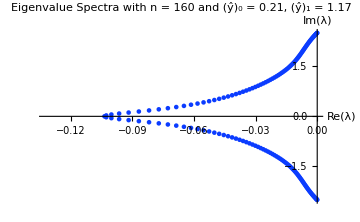

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsC6/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13};
RHSBoundaryList={a00,a01,a02,a03,a04,a10,a11,a12,a13,a14};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_C6","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP6R2DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.4963477370017426;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.04075360091710232;
		double a1 = 0.723439643221641;
		double a2 = 0.15683084734860173;
		double gamma01 =  - 3.531337876522152;
		double gamma02 =  - 11.2970068147929;
		double gamma10 = 0.16123050668544858;
		double gamma12 = 0.4741493035858441;
		double gamma13 =  - 0.038978437534430796;
		double a00 =  - 2.1419160987708987;
		double a01 = 14.474119440299228;
		double a02 =  - 8.297006814789217;
		double a03 =  - 4.4323356049301275;
		double a04 = 0.397139078188711;
		double a10 =  - 0.5431362438346228;
		double a11 =  - 0.5240000610825333;
		double a12 = 1.0747761362453676;
		double a13 =  - 0.0014084866408688862;
		double a14 =  - 0.006231344687109832;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04},
			{a10, a11, a12, a13, a14}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a2, -a1, 0.0, a1, a2
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_C6_yHat0_0.21_yHat1_1.17.h